### Code

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["SSSiCv100`"];
```

### Tests

Select a ruleset to investigate, possibly by giving its reduced rank index, giving it some convenient name:

```mathematica
rs01=FromReducedRankIndex[6308190100]
```

<|Index→6308190100,QCode→34243232424233,RuleSet→{AB→BA,AA→B,B→AAA}|>

We can pull out the ruleset itself:

```mathematica
rs01[["RuleSet"]]
```

{AB→BA,AA→B,B→AAA}

Or start from a ruleset, or from a QCode:

```mathematica
FromReducedRankRuleSet[{"AA"->"","AB"->"BA","A"->"BB","B"->"AAA"}]
```

<|Index→702927424475,QCode→31342432243424233,RuleSet→{AA→,AB→BA,A→BB,B→AAA}|>

We generate the sessie and its causal network, again giving it a convenient name:

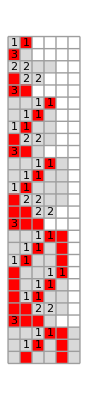



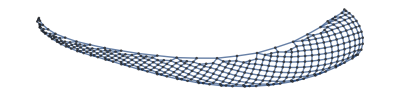
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss01=SSS[rs01[["RuleSet"]], "AB",800, (* choose an appropriate initial state string, and # steps *)
(* options *) Min->1,Max->400,SSSMin->Automatic,SSSMax->27,NetMin->Automatic,NetMax->384,HighlightMethod->Number,RulePlacement->Bottom,NetMethod->{GraphPlot},ImageSize->62.,NetSize->{Automatic,189.},SSSSize->{Automatic,250},IconSize->{Automatic,20},VertexSize->Automatic,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->False];(* options can be changed or omitted, but these are reasonable choices *)
```

BTW, new button in SSSInteractiveDisplay:

```mathematica
SSSInteractiveDisplay[sss01]
```

```mathematica
SSSDisplay[sss01,Min->1,Max->400,SSSMin->Automatic,SSSMax->27,NetMin->Automatic,NetMax->384,HighlightMethod->Number,RulePlacement->Bottom,NetMethod->{GraphPlot},ImageSize->62.,NetSize->{Automatic,189.},SSSSize->{Automatic,220},IconSize->{Automatic,20},VertexSize->Automatic,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->False]
```

Then we look at its Net, and create the list of lists of integers that we will summarize:

```mathematica
sss01[["Net"]]//Short
```

{1→2,2→3,2→3,2→4,1→4,3→5,5→6,4→6,5→7,6→7,«757»,395→396,394→397,396→397,395→398,370→398,396→399,398→399,397→400,399→400}

```mathematica
nds01=ToNetDifferenceSets[sss01[["Net"]]]
```

{{1,3},{1,1,2},{2},{2},{1,2,3},{1,9},{1,2},{1,2},{2},{1,2,3},{1,4},{1,2},{1,3},{3},{5},{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44},{1,2,3},{1,3},{1,3},{3,44},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,51},{1,2},{1,42},{44},{1,2,3},{1,3},{1,3},{3,45},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,4},{1,2},{1}}

You will probably need to limit the part of the nds list that you try to compact, omitting the incomplete sets at the end of the list. In theory it’s not needed to start later than the beginning of the list.

```mathematica
Position[nds01,44]
```

{{704,1},{708,2},{751,1}}

```mathematica
nds01[[1;;750]]
```

{{1,3},{1,1,2},{2},{2},{1,2,3},{1,9},{1,2},{1,2},{2},{1,2,3},{1,4},{1,2},{1,3},{3},{5},{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44},{1,2,3},{1,3},{1,3},{3,44},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,51},{1,2},{1,42}}

Try the reduction:

```mathematica
rsl01=ReduceSetList[nds01[[1;;750]]]
```

{{1,3},{1,1,2},€^2[{2}],{1,2,3},{1,9},€^2[{1,2}],{2},{1,2,3},{1,4},{1,2},{1,3},€_(n$1⊨1)^2[{3+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,44},€^13[€^2[{1,3}],{3,42}],{1,51},{1,2},{1,42}}

Look for most compressed part.  Nothing jumps out.  But from this point, I can easily finish the reduction manually.  Copy the result, add some extra lines (<Enter> key) to line up parts. We might use the near-repeated part  €_(n$1⊨1)^2[{??+2 (-1+n$1)}] for alignment:

```mathematica
{{1,3},
{1,1,2},€^2[{2}],{1,2,3},{1,9},€^2[{1,2}],{2},{1,2,3},{1,4},{1,2},{1,3},
€_(n$1⊨1)^2[{3+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},
€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},
€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},
€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},
€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},
€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},
€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},
€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},
€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},
€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},
€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},
€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},
€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},
...}
```

Most of those lines follow a clear pattern:

€_(k⊨1)^13[€_(j⊨1)^2[{3k+2 (-1+j)}],{1,2,3},€^2[{1,3}],{3,3k+2},€^(k-1)[€^2[{1,3}],{3,3k}],{1,3k+9},{1,2},{1,3k},{3k+2},{1,2,3},€^2[{1,3}],{3,3k+3},€^(k-1)[€^2[{1,3}],{3,k+1}],{1,4},{1,2},{1,3k+1}]

Can this work with k starting earlier?  No.

```mathematica
{3k+2 (-1+j)} /.k->-1 /.j->1//FullSimplify
```

{-3}

Get an editable version of that last complete line:

```mathematica
rsl01[[-24;;-9]]
```

{€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40}}

```mathematica
rsl01[[-24;;-9]]//InputForm
```

{IndexedConcatenate[{39 + 2*(-1 + n$1)}, {n$1, 1, 2}], {1, 2, 3}, IndexedConcatenate[{1, 3}, 2], {3, 41}, IndexedConcatenate[IndexedConcatenate[{1, 3}, 2], {3, 39}, 12], {1, 48}, {1, 2}, {1, 39}, {41}, {1, 2, 3}, IndexedConcatenate[{1, 3}, 2], {3, 42}, 
 IndexedConcatenate[IndexedConcatenate[{1, 3}, 2], {3, 40}, 12], {1, 4}, {1, 2}, {1, 40}}

```mathematica
Clear[k,j]
```

```mathematica
{
IndexedConcatenate[
IndexedConcatenate[{3k + 2(j-1)}, {j, 1, 2}], {1, 2, 3}, IndexedConcatenate[{1, 3}, 2], {3, 3k+2}, 
IndexedConcatenate[IndexedConcatenate[{1, 3}, 2], {3, 3k}, k-1], {1, 3k+9}, {1, 2}, {1, 3k}, {3k+2}, {1, 2, 3}, IndexedConcatenate[{1, 3}, 2], {3, 3k+3}, 
 IndexedConcatenate[IndexedConcatenate[{1, 3}, 2], {3, 3k+1}, 12], {1, 4}, {1, 2}, {1, 3k+1},
{k,1,13}]}
```

{€_(k⊨1)^13[€_(j⊨1)^2[{2 (j-1)+3 k}],{1,2,3},€^2[{1,3}],{3,3 k+2},€^(k-1)[€^2[{1,3}],{3,3 k}],{1,3 k+9},{1,2},{1,3 k},{3 k+2},{1,2,3},€^2[{1,3}],{3,3 k+3},€^12[€^2[{1,3}],{3,3 k+1}],{1,4},{1,2},{1,3 k+1}]}

```mathematica
{
IndexedConcatenate[
IndexedConcatenate[{3k + 2(j-1)}, {j, 1, 2}], {1, 2, 3}, IndexedConcatenate[{1, 3}, 2], {3, 3k+2}, 
IndexedConcatenate[IndexedConcatenate[{1, 3}, 2], {3, 3k}, k-1], {1, 3k+9}, {1, 2}, {1, 3k}, {3k+2}, {1, 2, 3}, IndexedConcatenate[{1, 3}, 2], {3, 3k+3}, 
 IndexedConcatenate[IndexedConcatenate[{1, 3}, 2], {3, 3k+1}, 12], {1, 4}, {1, 2}, {1, 3k+1},
{k,1,13}]}//Expand
```

{{3},{5},{1,2,3},{1,3},{1,3},{3,5},€^0[{1,3},{1,3},{3,3}],{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,3},{1,3},{3,4},{1,3},{1,3},{3,4},{1,3},{1,3},{3,4},{1,3},{1,3},{3,4},{1,3},{1,3},{3,4},{1,3},{1,3},{3,4},{1,3},{1,3},{3,4},{1,3},{1,3},{3,4},{1,3},{1,3},{3,4},{1,3},{1,3},{3,4},{1,3},{1,3},{3,4},{1,3},{1,3},{3,4},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},€^1[{1,3},{1,3},{3,6}],{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,3},{1,3},{3,7},{1,3},{1,3},{3,7},{1,3},{1,3},{3,7},{1,3},{1,3},{3,7},{1,3},{1,3},{3,7},{1,3},{1,3},{3,7},{1,3},{1,3},{3,7},{1,3},{1,3},{3,7},{1,3},{1,3},{3,7},{1,3},{1,3},{3,7},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},€^2[{1,3},{1,3},{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},€^3[{1,3},{1,3},{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},€^4[{1,3},{1,3},{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},€^5[{1,3},{1,3},{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},€^6[{1,3},{1,3},{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},€^7[{1,3},{1,3},{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},€^8[{1,3},{1,3},{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},€^9[{1,3},{1,3},{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},€^10[{1,3},{1,3},{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},€^11[{1,3},{1,3},{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},€^12[{1,3},{1,3},{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40}}

```mathematica
rsl01[[12;;15]]
```

{€_(n$1⊨1)^2[{3+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,5}}

```mathematica
GraphPlot[FromNetDifferenceSets@%]
```

#### Two Linear (1D) examples

```mathematica
FromReducedRankIndex[2]
```

<|Index→2,QCode→0,RuleSet→{A→,→A}|>

By the way, look at these patterns in the Reduced Rank Enumeration for SSSs:

```mathematica
FromReducedRankIndex /@ Range[50]//Column
```

<|Index→1,QCode→,RuleSet→{A→}|>
<|Index→2,QCode→0,RuleSet→{A→,→A}|>
<|Index→3,QCode→1,RuleSet→{A→,A→}|>
<|Index→4,QCode→2,RuleSet→{A→A}|>
<|Index→5,QCode→3,RuleSet→{AA→}|>
<|Index→6,QCode→4,RuleSet→{B→}|>
<|Index→7,QCode→00,RuleSet→{A→,→A,→,A→}|>
<|Index→8,QCode→01,RuleSet→{A→,→A,→A}|>
<|Index→9,QCode→02,RuleSet→{A→,→A,A→}|>
<|Index→10,QCode→03,RuleSet→{A→,→AA}|>
<|Index→11,QCode→04,RuleSet→{A→,→B}|>
<|Index→12,QCode→10,RuleSet→{A→,A→,→A}|>
<|Index→13,QCode→11,RuleSet→{A→,A→,A→}|>
<|Index→14,QCode→12,RuleSet→{A→,A→A}|>
<|Index→15,QCode→13,RuleSet→{A→,AA→}|>
<|Index→16,QCode→14,RuleSet→{A→,B→}|>
<|Index→17,QCode→20,RuleSet→{A→A,→,A→}|>
<|Index→18,QCode→21,RuleSet→{A→A,→A}|>
<|Index→19,QCode→22,RuleSet→{A→A,A→}|>
<|Index→20,QCode→23,RuleSet→{A→AA}|>
<|Index→21,QCode→24,RuleSet→{A→B}|>
<|Index→22,QCode→30,RuleSet→{AA→,→A}|>
<|Index→23,QCode→31,RuleSet→{AA→,A→}|>
<|Index→24,QCode→32,RuleSet→{AA→A}|>
<|Index→25,QCode→33,RuleSet→{AAA→}|>
<|Index→26,QCode→34,RuleSet→{AB→}|>
<|Index→27,QCode→40,RuleSet→{B→,→A}|>
<|Index→28,QCode→41,RuleSet→{B→,A→}|>
<|Index→29,QCode→42,RuleSet→{B→A}|>
<|Index→30,QCode→43,RuleSet→{BA→}|>
<|Index→31,QCode→44,RuleSet→{C→}|>
<|Index→32,QCode→000,RuleSet→{A→,→A,→,A→,→A}|>
<|Index→33,QCode→001,RuleSet→{A→,→A,→,A→,A→}|>
<|Index→34,QCode→002,RuleSet→{A→,→A,→,A→A}|>
<|Index→35,QCode→003,RuleSet→{A→,→A,→,AA→}|>
<|Index→36,QCode→004,RuleSet→{A→,→A,→,B→}|>
<|Index→37,QCode→010,RuleSet→{A→,→A,→A,→,A→}|>
<|Index→38,QCode→011,RuleSet→{A→,→A,→A,→A}|>
<|Index→39,QCode→012,RuleSet→{A→,→A,→A,A→}|>
<|Index→40,QCode→013,RuleSet→{A→,→A,→AA}|>
<|Index→41,QCode→014,RuleSet→{A→,→A,→B}|>
<|Index→42,QCode→020,RuleSet→{A→,→A,A→,→A}|>
<|Index→43,QCode→021,RuleSet→{A→,→A,A→,A→}|>
<|Index→44,QCode→022,RuleSet→{A→,→A,A→A}|>
<|Index→45,QCode→023,RuleSet→{A→,→A,AA→}|>
<|Index→46,QCode→024,RuleSet→{A→,→A,B→}|>
<|Index→47,QCode→030,RuleSet→{A→,→AA,→,A→}|>
<|Index→48,QCode→031,RuleSet→{A→,→AA,→A}|>
<|Index→49,QCode→032,RuleSet→{A→,→AA,A→}|>
<|Index→50,QCode→033,RuleSet→{A→,→AAA}|>

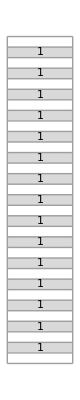
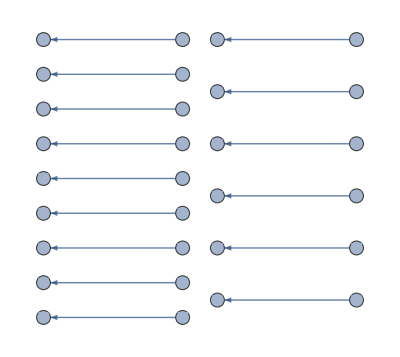
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
ssslin1=SSS[FromReducedRankIndex[2],"",30];
```

```mathematica
ssslin1[["Net"]]
```

{1→2,3→4,5→6,7→8,9→10,11→12,13→14,15→16,17→18,19→20,21→22,23→24,25→26,27→28,29→30}

```mathematica
ToNetDifferenceSets[ssslin1[["Net"]]]
```

{{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1},{},{1}}

```mathematica
ReduceSetList@%
```

{€^14[{1},{}],{1}}

Use most compact part:

```mathematica
{€^14[{1},{}]}
```

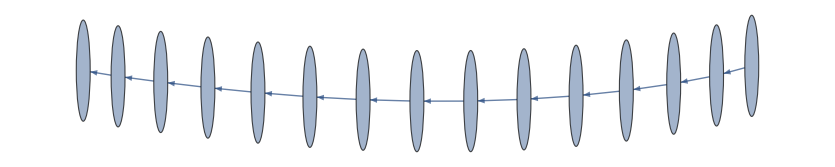
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

```mathematica
ssslin2=SSS[FromReducedRankIndex[4],"A",15,NetSize->550];
```

```mathematica
ssslin2[["Net"]]
```

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→10,10→11,11→12,12→13,13→14,14→15}

```mathematica
ToNetDifferenceSets[ssslin2[["Net"]]]
```

{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

```mathematica
ReduceSetList@%
```

{€^14[{1}]}

Note: pull up Jeanna Toulouse’s & Chris Trana’s posters, compare to their network summaries!

#### The 2D (mostly) hexagonal network

```mathematica
rsHex=FromReducedRankRuleSet[{"AA"->"BA","AB"->"AA","B"->"AA"}]
```

<|Index→1181262395,QCode→3243234232423,RuleSet→{AA→BA,AB→AA,B→AA}|>

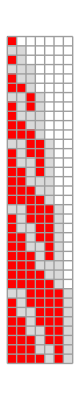
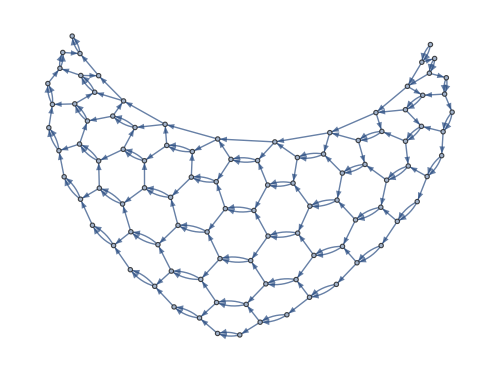
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sssHex=SSS[rsHex, "B",400, (* choose an appropriate initial state string, and # steps *)
(* options *) SSSMax->35,NetMax->100,NetSize->{500,Automatic},SSSSize->{Automatic,380},HighlightMethod->None,RulePlacement->Left,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True,ImageSize->304.,NetSize->{Automatic,338.},SSSSize->{Automatic,486.},IconSize->{Automatic,31.8},VertexSize->Automatic];
```

```mathematica
SSSInteractiveDisplay[sssHex]
```

```mathematica
sssHex["Distance"]
```

{0,1,2,3,2,4,5,3,4,3,6,7,5,6,4,5,4,8,9,7,8,6,7,5,6,5,10,11,9,10,8,9,7,8,6,7,6,12,13,11,12,10,11,9,10,8,9,7,8,7,14,15,13,14,12,13,11,12,10,11,9,10,8,9,8,16,17,15,16,14,15,13,14,12,13,11,12,10,11,9,10,9,18,19,17,18,16,17,15,16,14,15,13,14,12,13,11,12,10,11,10,20,21,19,20,18,19,17,18,16,17,15,16,14,15,13,14,12,13,11,12,11,22,23,21,22,20,21,19,20,18,19,17,18,16,17,15,16,14,15,13,14,12,13,12,24,25,23,24,22,23,21,22,20,21,19,20,18,19,17,18,16,17,15,16,14,15,13,14,13,26,27,25,26,24,25,23,24,22,23,21,22,20,21,19,20,18,19,17,18,16,17,15,16,14,15,14,28,29,27,28,26,27,25,26,24,25,23,24,22,23,21,22,20,21,19,20,18,19,17,18,16,17,15,16,15,30,31,29,30,28,29,27,28,26,27,25,26,24,25,23,24,22,23,21,22,20,21,19,20,18,19,17,18,16,17,16,32,33,31,32,30,31,29,30,28,29,27,28,26,27,25,26,24,25,23,24,22,23,21,22,20,21,19,20,18,19,17,18,17,34,35,33,34,32,33,31,32,30,31,29,30,28,29,27,28,26,27,25,26,24,25,23,24,22,23,21,22,20,21,19,20,18,19,18,36,37,35,36,34,35,33,34,32,33,31,32,30,31,29,30,28,29,27,28,26,27,25,26,24,25,23,24,22,23,21,22,20,21,19,20,19,38,39,37,38,36,37,35,36,34,35,33,34,32,33,31,32,30,31,29,30,28,29,27,28,26,27,25,26,24,25,23,24,22,23,21,22,20,21}

```mathematica
Tally[sssHex["Distance"]]
```

{{0,1},{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},{11,11},{12,12},{13,13},{14,14},{15,15},{16,16},{17,17},{18,18},{19,19},{20,19},{21,19},{22,18},{23,17},{24,16},{25,15},{26,14},{27,13},{28,12},{29,11},{30,10},{31,9},{32,8},{33,7},{34,6},{35,5},{36,4},{37,3},{38,2},{39,1}}

```mathematica
Tally[sssHex["Distance"]][[1;;20]]
```

{{0,1},{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},{11,11},{12,12},{13,13},{14,14},{15,15},{16,16},{17,17},{18,18},{19,19}}

```mathematica
Last/@%
```

{1,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19}

```mathematica
Accumulate[%]
```

{1,2,4,7,11,16,22,29,37,46,56,67,79,92,106,121,137,154,172,191}

```mathematica
NestList[Differences,%,2]//Grid
```

1 | 2 | 4 | 7 | 11 | 16 | 22 | 29 | 37 | 46 | 56 | 67 | 79 | 92 | 106 | 121 | 137 | 154 | 172 | 191
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  |

```mathematica
ToNetDifferenceSets[sssHex["Net"]]
```

{{1,1},{1,3},{1,1},{1,2},{3,5},{1,1},{1,4},{1,1},{1,4},{5,7},{1,1},{1,6},{1,1},{1,6},{1,1},{1,6},{7,9},{1,1},{1,8},{1,1},{1,8},{1,1},{1,8},{1,1},{1,8},{9,11},{1,1},{1,10},{1,1},{1,10},{1,1},{1,10},{1,1},{1,10},{1,1},{1,10},{11,13},{1,1},{1,12},{1,1},{1,12},{1,1},{1,12},{1,1},{1,12},{1,1},{1,12},{1,1},{1,12},{13,15},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{1,1},{1,14},{15,17},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{1,1},{1,16},{17,19},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{1,1},{1,18},{19,21},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{1,1},{1,20},{21,23},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{1,1},{1,22},{23,25},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{1,1},{1,24},{25,27},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{1,1},{1,26},{27,29},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{1,1},{1,28},{29,31},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{1,1},{1,30},{31,33},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{1,1},{1,32},{33,35},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{1,1},{1,34},{35,37},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{1,1},{1,36},{37},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1},{1},{1,1}}

```mathematica
ReduceSetList[%]
```

{€_(n$1⊨1)^2[{1,1},{1,4-n$1}],€_(n$1⊨1)^17[{1+2 n$1,3+2 n$1},€^(1+n$1)[{1,1},{1,2 (1+n$1)}]],{37},€^18[{1,1},{1}],{1,1}}

```mathematica
%26[[2]]
```

€_(n$1⊨1)^17[{1+2 n$1,3+2 n$1},€^(1+n$1)[{1,1},{1,2 (1+n$1)}]]

```mathematica
%26[[2]] /. n$1->k /. k->k-1//Simplify
```

€_(k-1⊨1)^17[{2 k-1,2 k+1},€^k[{1,1},{1,2 k}]]

```mathematica
%26[[2]] //InputForm
```

IndexedConcatenate[{1 + 2*n$1, 3 + 2*n$1}, IndexedConcatenate[{1, 1}, {1, 2*(1 + n$1)}, 1 + n$1], {n$1, 1, 17}]

```mathematica
IndexedConcatenate[{2k-1, 2k+1}, IndexedConcatenate[{1, 1}, {1, 2k}, k], {k, 1, 18}]
```

€_(k⊨1)^18[{2 k-1,2 k+1},€^k[{1,1},{1,2 k}]]

```mathematica
{ExpandAll[%34]}
```

```mathematica
GraphPlot@FromNetDifferenceSets@{ExpandAll[%34]}
```

-Graphics-